## Лабораторная работа №5 Гаврилюк Рената, ПО3

## Задание 1

Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3                5
```

15

```mathematica
2+   7
```

9

```mathematica
2/3
```

2/3

Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
17^(1/2)
```

√17

```mathematica
3      /7
```

3/7

Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
17.          ^(1/2)
```

4.12311

Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
3                   (6 +  5 )
```

33

## Задание 2

С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
N[e^(x *Sqrt[163]), 40]
```

e^(12.76714533480370466171095200978089234738 x)

Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

Справедливо ли неравенство

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E, 100]
N[E^Pi, 100]
```

22.45915771836104547342715220454373502758931513399669224920300255406692604039911791231851975272714303

23.14069263277926900572908636794854738026610624260021199344504640952434235069045278351697199706754922

## Задание 3

Решить уравнения

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумать свою

```mathematica
NSolve[{(4 x^2+y^2+4 y)/(y^2-4y)==4, x^3 y+y^4+x^4== 48}, {x,y}]
```

{{x→-0.0469283-3.60646 ⅈ,y→3.24297-2.49724 ⅈ},{x→-0.0469283+3.60646 ⅈ,y→3.24297+2.49724 ⅈ},{x→-2.39966,y→-1.00129},{x→2.23419-4.52611 ⅈ,y→0.246379+4.36771 ⅈ},{x→2.23419+4.52611 ⅈ,y→0.246379-4.36771 ⅈ},{x→-0.242495-2.43791 ⅈ,y→1.47718-0.424665 ⅈ},{x→-0.242495+2.43791 ⅈ,y→1.47718+0.424665 ⅈ},{x→3.03624,y→-1.50431}}

## Задание 4 Вариант 5 и 6

```mathematica
FindRoot[x^4-5x+2 == Exp[x-1], {x, 0,2}]
```

{x→0.302137}

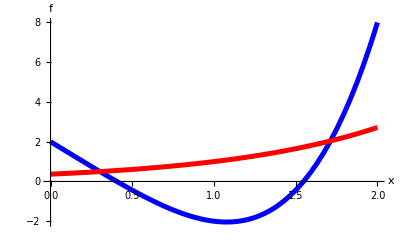

```mathematica
Plot[{x^4-5x+2, Exp[x-1]}, {x, 0,2}, PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "f"}]
```

```mathematica
FindRoot[x^4-5x+2 == Exp[x-1], {x, 0.3}]
```

{x→0.302137}

```mathematica
FindRoot[x^4-5x+2 == Exp[x-1], {x, 1.7}]
```

{x→1.71259}

```mathematica
FindRoot[x^2+E^-x-2==Sin[2x], {x,-1,2}]
```

{x→-0.29875}

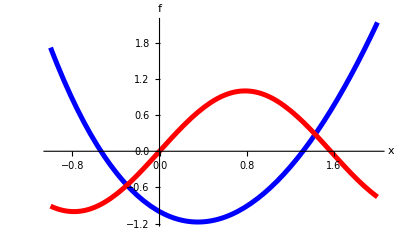

```mathematica
Plot[{x^2+E^-x-2, Sin[2x]}, {x, -1,2}, PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "f"}]
```

```mathematica
FindRoot[x^2+E^-x-2==Sin[2x], {x, -0.3}]
```

{x→-0.29875}

```mathematica
FindRoot[x^2+E^-x-2==Sin[2x], {x, 1.42}]
```

{x→1.42861}

## Задание 5 решение дифф уравнения

```mathematica
sol1=NDSolve[{y''[x]+2y'[x]  Cos[x]+5y [x]==0, y[0]==0, y'[0]==1},y, {x,0,5}]
```

{{y→InterpolatingFunction[…]}}

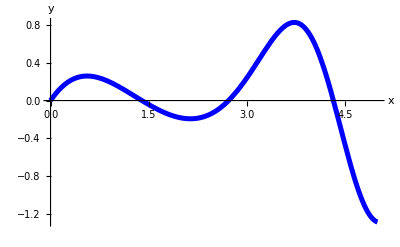

```mathematica
Plot[y[x]/.sol1, {x,0,5}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
sol2=FindRoot[(y[x]/.sol1[[1]])==0, {x,1.35}]
```

{x→1.39689}

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2
```

-0.417266

```mathematica
sol5 = FindRoot[D[y[x]/.sol1[[1]],x]==0, {x,2.1}]
```

{x→2.14018}

```mathematica
y[x]/.sol1[[1]]/.sol5
```

-0.192554

```mathematica
FindMinimum[y[x]/.sol1[[1]], {x,2.1}]
```

{-0.192554,{x→2.14018}}

```mathematica
sol10=NDSolve[{y''[x]+y'[x]  Tan[x]- Sin[x]==0, y[0]==-1, y'[0]==2},y, {x,0,9}]
```

{{y→InterpolatingFunction[…]}}

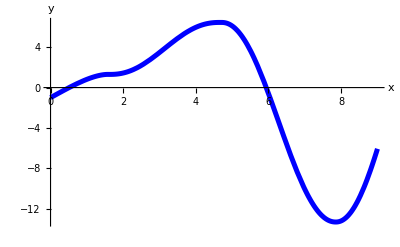

```mathematica
Plot[y[x]/.sol10, {x,0,9}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
sol11=FindRoot[(y[x]/.sol10[[1]])==0, {x,5.9}]
```

{x→5.93897}

```mathematica
D[y[x]/.sol10[[1]],x]/.sol11
```

-9.54781

```mathematica
sol12=FindRoot[D[y[x]/.sol10[[1]],x]==0, {x,7.8}]
```

{x→7.85394}

```mathematica
y[x]/.sol10[[1]]/.sol12
```

-13.3329

```mathematica
FindMinimum[y[x]/.sol10[[1]], {x,8}]
```

{-13.3329,{x→7.85394}}

## Задание 6 Вариант 1 и 2

```mathematica
task1 = Table[{x,(21+52x+73 x^2+17 x^3+33 x^4)(1+Random[Real, {-0.2,0.2}])}, {x,0,5,0.25}]
```

{{0.,22.3654},{0.25,33.5272},{0.5,82.9205},{0.75,111.98},{1.,182.074},{1.25,339.679},{1.5,563.766},{1.75,822.283},{2.,866.735},{2.25,1754.26},{2.5,1801.8},{2.75,2512.1},{3.,4539.73},{3.25,5701.47},{3.5,6767.6},{3.75,9179.46},{4.,10046.5},{4.25,13850.},{4.5,16102.1},{4.75,20970.8},{5.,27930.2}}

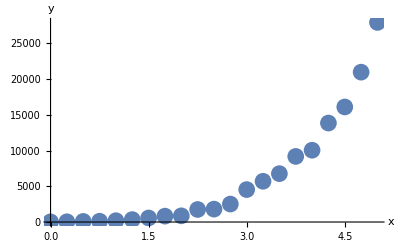

```mathematica
taskPlot=ListPlot[task1, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

```mathematica
y3=Fit[task1, {1,x,x^2, x^3, x^4},x]
```

306.355-1830.28 x+2206.5 x^2-762.787 x^3+121.738 x^4

```mathematica
y4=Fit[task1, {1,x,x^2, x^3, x^4},x]
```

306.355-1830.28 x+2206.5 x^2-762.787 x^3+121.738 x^4

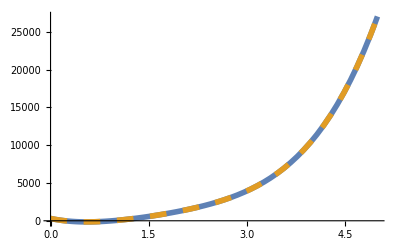

```mathematica
plot2 =Plot[{y3,y4}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

```mathematica
task2 = Table[{x,(21+42x+84Sin[x]+35Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,58.7315},{0.25,89.6086},{0.5,102.192},{0.75,137.391},{1.,146.154},{1.25,177.326},{1.5,159.201},{1.75,179.911},{2.,157.441},{2.25,149.119},{2.5,150.557},{2.75,147.663},{3.,123.843},{3.25,110.888},{3.5,96.7962},{3.75,109.727},{4.,97.9823},{4.25,108.099},{4.5,128.356},{4.75,128.079},{5.,171.263}}

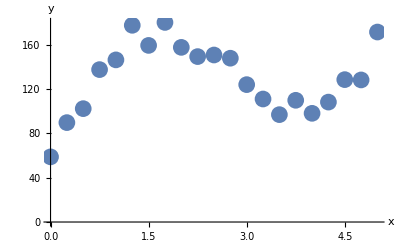

```mathematica
task2Plot=ListPlot[task2, PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[task2, {1,x,Cos[x], Sin[x]},x]
```

19.1313+42.7719 x+36.4008 Cos[x]+83.7551 Sin[x]

```mathematica
y2=Fit[task2, {1,x,x^2, x^3, x^4},x]
```

54.7101+144.464 x-48.3307 x^2-0.407449 x^3+1.04401 x^4

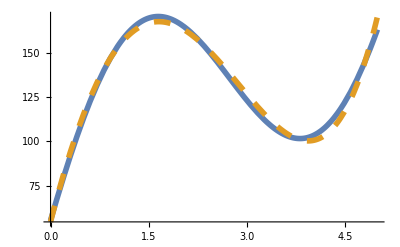

```mathematica
plot2 =Plot[{y1,y2}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

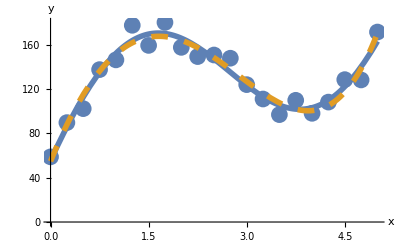

```mathematica
Show[task2Plot, plot2]
```